```mathematica
pp[4]
```

0

```mathematica
pp[3]
```

1

```mathematica
PP[100,1,1]
```

52513/720

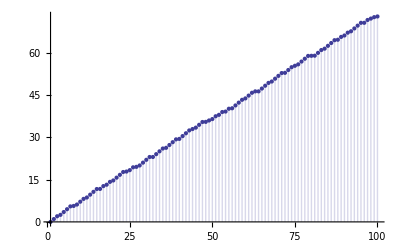

```mathematica
DiscretePlot[ PP[n,1,1],{n,1,100}]
```

```mathematica
ppAlt[n_,z_]:=Product[z^p[[2]]/(p[[2]]!),{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
pp[n_]:=If[PrimeQ[n],1,0]
PP[n_,k_, t_] := PP[n,k,t]=Sum[ t pp[j](1/(k!) + PP[Floor[n/j],k+1,t]),{j,2,n}]
PS[n_,k_] := PP[n,1,k]-PP[n-1,1,k]
Table[{ n=m,PS[n,1],PS[n,2], PS[n,3], PS[n,4], ppAlt[n,1], ppAlt[n,2], ppAlt[n,3], ppAlt[n,4]},{m,2,100}]//TableForm
```

2 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
3 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
4 | 1/2 | 2 | 9/2 | 8 | -1/2 | 2 | 9/2 | 8
5 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
6 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
7 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
8 | 1/6 | 4/3 | 9/2 | 32/3 | -ⅈ/6 | 4/3 | 9/2 | 32/3
9 | 1/2 | 2 | 9/2 | 8 | -1/2 | 2 | 9/2 | 8
10 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
11 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
12 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
13 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
14 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
15 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
16 | 1/24 | 2/3 | 27/8 | 32/3 | 1/24 | 2/3 | 27/8 | 32/3
17 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
18 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
19 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
20 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
21 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
22 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
23 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
24 | 1/6 | 8/3 | 27/2 | 128/3 | 1/6 | 8/3 | 27/2 | 128/3
25 | 1/2 | 2 | 9/2 | 8 | -1/2 | 2 | 9/2 | 8
26 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
27 | 1/6 | 4/3 | 9/2 | 32/3 | -ⅈ/6 | 4/3 | 9/2 | 32/3
28 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
29 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
30 | 1 | 8 | 27 | 64 | -ⅈ | 8 | 27 | 64
31 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
32 | 1/120 | 4/15 | 81/40 | 128/15 | ⅈ/120 | 4/15 | 81/40 | 128/15
33 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
34 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
35 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
36 | 1/4 | 4 | 81/4 | 64 | 1/4 | 4 | 81/4 | 64
37 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
38 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
39 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
40 | 1/6 | 8/3 | 27/2 | 128/3 | 1/6 | 8/3 | 27/2 | 128/3
41 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
42 | 1 | 8 | 27 | 64 | -ⅈ | 8 | 27 | 64
43 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
44 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
45 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
46 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
47 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
48 | 1/24 | 4/3 | 81/8 | 128/3 | ⅈ/24 | 4/3 | 81/8 | 128/3
49 | 1/2 | 2 | 9/2 | 8 | -1/2 | 2 | 9/2 | 8
50 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
51 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
52 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
53 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
54 | 1/6 | 8/3 | 27/2 | 128/3 | 1/6 | 8/3 | 27/2 | 128/3
55 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
56 | 1/6 | 8/3 | 27/2 | 128/3 | 1/6 | 8/3 | 27/2 | 128/3
57 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
58 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
59 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
60 | 1/2 | 8 | 81/2 | 128 | 1/2 | 8 | 81/2 | 128
61 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
62 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
63 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
64 | 1/720 | 4/45 | 81/80 | 256/45 | -1/720 | 4/45 | 81/80 | 256/45
65 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
66 | 1 | 8 | 27 | 64 | -ⅈ | 8 | 27 | 64
67 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
68 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
69 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
70 | 1 | 8 | 27 | 64 | -ⅈ | 8 | 27 | 64
71 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
72 | 1/12 | 8/3 | 81/4 | 256/3 | ⅈ/12 | 8/3 | 81/4 | 256/3
73 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
74 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
75 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
76 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
77 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
78 | 1 | 8 | 27 | 64 | -ⅈ | 8 | 27 | 64
79 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
80 | 1/24 | 4/3 | 81/8 | 128/3 | ⅈ/24 | 4/3 | 81/8 | 128/3
81 | 1/24 | 2/3 | 27/8 | 32/3 | 1/24 | 2/3 | 27/8 | 32/3
82 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
83 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
84 | 1/2 | 8 | 81/2 | 128 | 1/2 | 8 | 81/2 | 128
85 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
86 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
87 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
88 | 1/6 | 8/3 | 27/2 | 128/3 | 1/6 | 8/3 | 27/2 | 128/3
89 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
90 | 1/2 | 8 | 81/2 | 128 | 1/2 | 8 | 81/2 | 128
91 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
92 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
93 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
94 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
95 | 1 | 4 | 9 | 16 | -1 | 4 | 9 | 16
96 | 1/120 | 8/15 | 243/40 | 512/15 | -1/120 | 8/15 | 243/40 | 512/15
97 | 1 | 2 | 3 | 4 | ⅈ | 2 | 3 | 4
98 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
99 | 1/2 | 4 | 27/2 | 32 | -ⅈ/2 | 4 | 27/2 | 32
100 | 1/4 | 4 | 81/4 | 64 | 1/4 | 4 | 81/4 | 64

```mathematica
512*128
```

65536

```mathematica
8!
```

40320

```mathematica
(z^aa)/(aa!)
```

z^aa/(aa!)

```mathematica
Table[{ n=m,ppAlt[n,1], ppAlt[n,-1], ppAlt[n,I], ppAlt[n,-I]},{m,2,100}]//TableForm
```

2 | 1 | -1 | ⅈ | -ⅈ
3 | 1 | -1 | ⅈ | -ⅈ
4 | 1/2 | 1/2 | -1/2 | -1/2
5 | 1 | -1 | ⅈ | -ⅈ
6 | 1 | 1 | -1 | -1
7 | 1 | -1 | ⅈ | -ⅈ
8 | 1/6 | -1/6 | -ⅈ/6 | ⅈ/6
9 | 1/2 | 1/2 | -1/2 | -1/2
10 | 1 | 1 | -1 | -1
11 | 1 | -1 | ⅈ | -ⅈ
12 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
13 | 1 | -1 | ⅈ | -ⅈ
14 | 1 | 1 | -1 | -1
15 | 1 | 1 | -1 | -1
16 | 1/24 | 1/24 | 1/24 | 1/24
17 | 1 | -1 | ⅈ | -ⅈ
18 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
19 | 1 | -1 | ⅈ | -ⅈ
20 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
21 | 1 | 1 | -1 | -1
22 | 1 | 1 | -1 | -1
23 | 1 | -1 | ⅈ | -ⅈ
24 | 1/6 | 1/6 | 1/6 | 1/6
25 | 1/2 | 1/2 | -1/2 | -1/2
26 | 1 | 1 | -1 | -1
27 | 1/6 | -1/6 | -ⅈ/6 | ⅈ/6
28 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
29 | 1 | -1 | ⅈ | -ⅈ
30 | 1 | -1 | -ⅈ | ⅈ
31 | 1 | -1 | ⅈ | -ⅈ
32 | 1/120 | -1/120 | ⅈ/120 | -ⅈ/120
33 | 1 | 1 | -1 | -1
34 | 1 | 1 | -1 | -1
35 | 1 | 1 | -1 | -1
36 | 1/4 | 1/4 | 1/4 | 1/4
37 | 1 | -1 | ⅈ | -ⅈ
38 | 1 | 1 | -1 | -1
39 | 1 | 1 | -1 | -1
40 | 1/6 | 1/6 | 1/6 | 1/6
41 | 1 | -1 | ⅈ | -ⅈ
42 | 1 | -1 | -ⅈ | ⅈ
43 | 1 | -1 | ⅈ | -ⅈ
44 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
45 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
46 | 1 | 1 | -1 | -1
47 | 1 | -1 | ⅈ | -ⅈ
48 | 1/24 | -1/24 | ⅈ/24 | -ⅈ/24
49 | 1/2 | 1/2 | -1/2 | -1/2
50 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
51 | 1 | 1 | -1 | -1
52 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
53 | 1 | -1 | ⅈ | -ⅈ
54 | 1/6 | 1/6 | 1/6 | 1/6
55 | 1 | 1 | -1 | -1
56 | 1/6 | 1/6 | 1/6 | 1/6
57 | 1 | 1 | -1 | -1
58 | 1 | 1 | -1 | -1
59 | 1 | -1 | ⅈ | -ⅈ
60 | 1/2 | 1/2 | 1/2 | 1/2
61 | 1 | -1 | ⅈ | -ⅈ
62 | 1 | 1 | -1 | -1
63 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
64 | 1/720 | 1/720 | -1/720 | -1/720
65 | 1 | 1 | -1 | -1
66 | 1 | -1 | -ⅈ | ⅈ
67 | 1 | -1 | ⅈ | -ⅈ
68 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
69 | 1 | 1 | -1 | -1
70 | 1 | -1 | -ⅈ | ⅈ
71 | 1 | -1 | ⅈ | -ⅈ
72 | 1/12 | -1/12 | ⅈ/12 | -ⅈ/12
73 | 1 | -1 | ⅈ | -ⅈ
74 | 1 | 1 | -1 | -1
75 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
76 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
77 | 1 | 1 | -1 | -1
78 | 1 | -1 | -ⅈ | ⅈ
79 | 1 | -1 | ⅈ | -ⅈ
80 | 1/24 | -1/24 | ⅈ/24 | -ⅈ/24
81 | 1/24 | 1/24 | 1/24 | 1/24
82 | 1 | 1 | -1 | -1
83 | 1 | -1 | ⅈ | -ⅈ
84 | 1/2 | 1/2 | 1/2 | 1/2
85 | 1 | 1 | -1 | -1
86 | 1 | 1 | -1 | -1
87 | 1 | 1 | -1 | -1
88 | 1/6 | 1/6 | 1/6 | 1/6
89 | 1 | -1 | ⅈ | -ⅈ
90 | 1/2 | 1/2 | 1/2 | 1/2
91 | 1 | 1 | -1 | -1
92 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
93 | 1 | 1 | -1 | -1
94 | 1 | 1 | -1 | -1
95 | 1 | 1 | -1 | -1
96 | 1/120 | 1/120 | -1/120 | -1/120
97 | 1 | -1 | ⅈ | -ⅈ
98 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
99 | 1/2 | -1/2 | -ⅈ/2 | ⅈ/2
100 | 1/4 | 1/4 | 1/4 | 1/4

```mathematica
Table[{ n=m,ppAlt[n,(2^(-1/2))+(2^(-1/2)I)], ppAlt[n,-(2^(-1/2))+(2^(-1/2)I)], ppAlt[n,-(2^(-1/2))-(2^(-1/2)I)], ppAlt[n,(2^(-1/2))-(2^(-1/2)I)]},{m,2,100}]//TableForm
```

2 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
3 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
4 | ⅈ/2 | -ⅈ/2 | ⅈ/2 | -ⅈ/2
5 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
6 | ⅈ | -ⅈ | ⅈ | -ⅈ
7 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
8 | -(1/6-ⅈ/6)/(√2) | (1/6+ⅈ/6)/(√2) | (1/6-ⅈ/6)/(√2) | -(1/6+ⅈ/6)/(√2)
9 | ⅈ/2 | -ⅈ/2 | ⅈ/2 | -ⅈ/2
10 | ⅈ | -ⅈ | ⅈ | -ⅈ
11 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
12 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
13 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
14 | ⅈ | -ⅈ | ⅈ | -ⅈ
15 | ⅈ | -ⅈ | ⅈ | -ⅈ
16 | -1/24 | -1/24 | -1/24 | -1/24
17 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
18 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
19 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
20 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
21 | ⅈ | -ⅈ | ⅈ | -ⅈ
22 | ⅈ | -ⅈ | ⅈ | -ⅈ
23 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
24 | -1/6 | -1/6 | -1/6 | -1/6
25 | ⅈ/2 | -ⅈ/2 | ⅈ/2 | -ⅈ/2
26 | ⅈ | -ⅈ | ⅈ | -ⅈ
27 | -(1/6-ⅈ/6)/(√2) | (1/6+ⅈ/6)/(√2) | (1/6-ⅈ/6)/(√2) | -(1/6+ⅈ/6)/(√2)
28 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
29 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
30 | -(1-ⅈ)/(√2) | (1+ⅈ)/(√2) | (1-ⅈ)/(√2) | -(1+ⅈ)/(√2)
31 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
32 | -(1/120+ⅈ/120)/(√2) | (1/120-ⅈ/120)/(√2) | (1/120+ⅈ/120)/(√2) | -(1/120-ⅈ/120)/(√2)
33 | ⅈ | -ⅈ | ⅈ | -ⅈ
34 | ⅈ | -ⅈ | ⅈ | -ⅈ
35 | ⅈ | -ⅈ | ⅈ | -ⅈ
36 | -1/4 | -1/4 | -1/4 | -1/4
37 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
38 | ⅈ | -ⅈ | ⅈ | -ⅈ
39 | ⅈ | -ⅈ | ⅈ | -ⅈ
40 | -1/6 | -1/6 | -1/6 | -1/6
41 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
42 | -(1-ⅈ)/(√2) | (1+ⅈ)/(√2) | (1-ⅈ)/(√2) | -(1+ⅈ)/(√2)
43 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
44 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
45 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
46 | ⅈ | -ⅈ | ⅈ | -ⅈ
47 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
48 | -(1/24+ⅈ/24)/(√2) | (1/24-ⅈ/24)/(√2) | (1/24+ⅈ/24)/(√2) | -(1/24-ⅈ/24)/(√2)
49 | ⅈ/2 | -ⅈ/2 | ⅈ/2 | -ⅈ/2
50 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
51 | ⅈ | -ⅈ | ⅈ | -ⅈ
52 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
53 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
54 | -1/6 | -1/6 | -1/6 | -1/6
55 | ⅈ | -ⅈ | ⅈ | -ⅈ
56 | -1/6 | -1/6 | -1/6 | -1/6
57 | ⅈ | -ⅈ | ⅈ | -ⅈ
58 | ⅈ | -ⅈ | ⅈ | -ⅈ
59 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
60 | -1/2 | -1/2 | -1/2 | -1/2
61 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
62 | ⅈ | -ⅈ | ⅈ | -ⅈ
63 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
64 | -ⅈ/720 | ⅈ/720 | -ⅈ/720 | ⅈ/720
65 | ⅈ | -ⅈ | ⅈ | -ⅈ
66 | -(1-ⅈ)/(√2) | (1+ⅈ)/(√2) | (1-ⅈ)/(√2) | -(1+ⅈ)/(√2)
67 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
68 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
69 | ⅈ | -ⅈ | ⅈ | -ⅈ
70 | -(1-ⅈ)/(√2) | (1+ⅈ)/(√2) | (1-ⅈ)/(√2) | -(1+ⅈ)/(√2)
71 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
72 | -(1/12+ⅈ/12)/(√2) | (1/12-ⅈ/12)/(√2) | (1/12+ⅈ/12)/(√2) | -(1/12-ⅈ/12)/(√2)
73 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
74 | ⅈ | -ⅈ | ⅈ | -ⅈ
75 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
76 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
77 | ⅈ | -ⅈ | ⅈ | -ⅈ
78 | -(1-ⅈ)/(√2) | (1+ⅈ)/(√2) | (1-ⅈ)/(√2) | -(1+ⅈ)/(√2)
79 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
80 | -(1/24+ⅈ/24)/(√2) | (1/24-ⅈ/24)/(√2) | (1/24+ⅈ/24)/(√2) | -(1/24-ⅈ/24)/(√2)
81 | -1/24 | -1/24 | -1/24 | -1/24
82 | ⅈ | -ⅈ | ⅈ | -ⅈ
83 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
84 | -1/2 | -1/2 | -1/2 | -1/2
85 | ⅈ | -ⅈ | ⅈ | -ⅈ
86 | ⅈ | -ⅈ | ⅈ | -ⅈ
87 | ⅈ | -ⅈ | ⅈ | -ⅈ
88 | -1/6 | -1/6 | -1/6 | -1/6
89 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
90 | -1/2 | -1/2 | -1/2 | -1/2
91 | ⅈ | -ⅈ | ⅈ | -ⅈ
92 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
93 | ⅈ | -ⅈ | ⅈ | -ⅈ
94 | ⅈ | -ⅈ | ⅈ | -ⅈ
95 | ⅈ | -ⅈ | ⅈ | -ⅈ
96 | -ⅈ/120 | ⅈ/120 | -ⅈ/120 | ⅈ/120
97 | (1+ⅈ)/(√2) | -(1-ⅈ)/(√2) | -(1+ⅈ)/(√2) | (1-ⅈ)/(√2)
98 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
99 | -(1/2-ⅈ/2)/(√2) | (1/2+ⅈ/2)/(√2) | (1/2-ⅈ/2)/(√2) | -(1/2+ⅈ/2)/(√2)
100 | -1/4 | -1/4 | -1/4 | -1/4

```mathematica
N[Cos[Pi/4]]
```

0.707107

```mathematica
N[1/Sqrt[2]]
```

0.707107

```mathematica
N[2^(-1/2)]
```

0.707107

```mathematica
liouville[n_,z_]:=Product[(-1)^p[[2]] Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Liou2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j] liouville[n,j],{j,0,k}]
LiouLinnik[n_]:=Sum[(-1)^(k+1)/k Liou2[n,k],{k,1,Log[2,n]}]
Table[{n,liouville[n,1],LiouLinnik[n]},{n,2,100}]//TableForm
```

2 | -1 | -1
3 | -1 | -1
4 | 1 | 1/2
5 | -1 | -1
6 | 1 | 0
7 | -1 | -1
8 | -1 | -1/3
9 | 1 | 1/2
10 | 1 | 0
11 | -1 | -1
12 | -1 | 0
13 | -1 | -1
14 | 1 | 0
15 | 1 | 0
16 | 1 | 1/4
17 | -1 | -1
18 | -1 | 0
19 | -1 | -1
20 | -1 | 0
21 | 1 | 0
22 | 1 | 0
23 | -1 | -1
24 | 1 | 0
25 | 1 | 1/2
26 | 1 | 0
27 | -1 | -1/3
28 | -1 | 0
29 | -1 | -1
30 | -1 | 0
31 | -1 | -1
32 | -1 | -1/5
33 | 1 | 0
34 | 1 | 0
35 | 1 | 0
36 | 1 | 0
37 | -1 | -1
38 | 1 | 0
39 | 1 | 0
40 | 1 | 0
41 | -1 | -1
42 | -1 | 0
43 | -1 | -1
44 | -1 | 0
45 | -1 | 0
46 | 1 | 0
47 | -1 | -1
48 | -1 | 0
49 | 1 | 1/2
50 | -1 | 0
51 | 1 | 0
52 | -1 | 0
53 | -1 | -1
54 | 1 | 0
55 | 1 | 0
56 | 1 | 0
57 | 1 | 0
58 | 1 | 0
59 | -1 | -1
60 | 1 | 0
61 | -1 | -1
62 | 1 | 0
63 | -1 | 0
64 | 1 | 1/6
65 | 1 | 0
66 | -1 | 0
67 | -1 | -1
68 | -1 | 0
69 | 1 | 0
70 | -1 | 0
71 | -1 | -1
72 | -1 | 0
73 | -1 | -1
74 | 1 | 0
75 | -1 | 0
76 | -1 | 0
77 | 1 | 0
78 | -1 | 0
79 | -1 | -1
80 | -1 | 0
81 | 1 | 1/4
82 | 1 | 0
83 | -1 | -1
84 | 1 | 0
85 | 1 | 0
86 | 1 | 0
87 | 1 | 0
88 | 1 | 0
89 | -1 | -1
90 | 1 | 0
91 | 1 | 0
92 | -1 | 0
93 | 1 | 0
94 | 1 | 0
95 | 1 | 0
96 | 1 | 0
97 | -1 | -1
98 | -1 | 0
99 | -1 | 0
100 | 1 | 0

```mathematica
liouville[n_,z_]:=Product[(-1)^p[[2]] Pochhammer[z,a=p[[2]]]/a!,{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Liou2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j] liouville[n,j],{j,0,k}]
LiouLinnik[n_]:=Sum[(-1)^(k+1)/k Liou2[n,k],{k,1,Log[2,n]}]
Table[{n,liouville[n,1],LiouLinnik[n]},{n,2,100}]//TableForm
```

```mathematica
(*totient*)
PrimeK[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
d[n_,k_]:=d[n,k]=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=EulerPhi[n];d[n_,0]:=0;d[1,0]:=1
d2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]d[n,j],{j,0,k}]
Linnik[n_]:=Linnik[n] = Sum[(-1)^(k+1)/k d2[n,k],{k,1,Log[2,n]}]
Table[{n,(n-1)PrimeK[n], Linnik[n]},{n,2,100}]//TableForm
```

2 | 1 | 1
3 | 2 | 2
4 | 3/2 | 3/2
5 | 4 | 4
6 | 0 | 0
7 | 6 | 6
8 | 7/3 | 7/3
9 | 4 | 4
10 | 0 | 0
11 | 10 | 10
12 | 0 | 0
13 | 12 | 12
14 | 0 | 0
15 | 0 | 0
16 | 15/4 | 15/4
17 | 16 | 16
18 | 0 | 0
19 | 18 | 18
20 | 0 | 0
21 | 0 | 0
22 | 0 | 0
23 | 22 | 22
24 | 0 | 0
25 | 12 | 12
26 | 0 | 0
27 | 26/3 | 26/3
28 | 0 | 0
29 | 28 | 28
30 | 0 | 0
31 | 30 | 30
32 | 31/5 | 31/5
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 36 | 36
38 | 0 | 0
39 | 0 | 0
40 | 0 | 0
41 | 40 | 40
42 | 0 | 0
43 | 42 | 42
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 46 | 46
48 | 0 | 0
49 | 24 | 24
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 52 | 52
54 | 0 | 0
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 58 | 58
60 | 0 | 0
61 | 60 | 60
62 | 0 | 0
63 | 0 | 0
64 | 21/2 | 21/2
65 | 0 | 0
66 | 0 | 0
67 | 66 | 66
68 | 0 | 0
69 | 0 | 0
70 | 0 | 0
71 | 70 | 70
72 | 0 | 0
73 | 72 | 72
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 0 | 0
78 | 0 | 0
79 | 78 | 78
80 | 0 | 0
81 | 20 | 20
82 | 0 | 0
83 | 82 | 82
84 | 0 | 0
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 0 | 0
89 | 88 | 88
90 | 0 | 0
91 | 0 | 0
92 | 0 | 0
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 96 | 96
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

```mathematica
(*totient*)
PrimeK[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
d[n_,k_]:=d[n,k]=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=EulerPhi[n];d[n_,0]:=0;d[1,0]:=1
d2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]d[n,j],{j,0,k}]
Linnik[n_]:=Linnik[n] = Sum[(-1)^(k+1)/k d2[n,k],{k,1,Log[2,n]}]
Table[{n,(n-1)PrimeK[n], Linnik[n]},{n,2,100}]//TableForm
```

```mathematica
ClearAll["Global`*"]
PrimeK[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
d[n_,k_]:=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=Abs[MoebiusMu[n]];d[n_,0]:=0;d[1,0]:=1
d2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]d[n,j],{j,0,k}]
Linnik[n_]:=Sum[(-1)^(k+1)/k d2[n,k],{k,1,Log[2,n]}]
Table[{n,-PrimeK[n] LiouvilleLambda[n],Linnik[n]},{n,2,100}]//TableForm
```

2 | 1 | 1
3 | 1 | 1
4 | -1/2 | -1/2
5 | 1 | 1
6 | 0 | 0
7 | 1 | 1
8 | 1/3 | 1/3
9 | -1/2 | -1/2
10 | 0 | 0
11 | 1 | 1
12 | 0 | 0
13 | 1 | 1
14 | 0 | 0
15 | 0 | 0
16 | -1/4 | -1/4
17 | 1 | 1
18 | 0 | 0
19 | 1 | 1
20 | 0 | 0
21 | 0 | 0
22 | 0 | 0
23 | 1 | 1
24 | 0 | 0
25 | -1/2 | -1/2
26 | 0 | 0
27 | 1/3 | 1/3
28 | 0 | 0
29 | 1 | 1
30 | 0 | 0
31 | 1 | 1
32 | 1/5 | 1/5
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 0 | 0
37 | 1 | 1
38 | 0 | 0
39 | 0 | 0
40 | 0 | 0
41 | 1 | 1
42 | 0 | 0
43 | 1 | 1
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 1 | 1
48 | 0 | 0
49 | -1/2 | -1/2
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 1 | 1
54 | 0 | 0
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 1 | 1
60 | 0 | 0
61 | 1 | 1
62 | 0 | 0
63 | 0 | 0
64 | -1/6 | -1/6
65 | 0 | 0
66 | 0 | 0
67 | 1 | 1
68 | 0 | 0
69 | 0 | 0
70 | 0 | 0
71 | 1 | 1
72 | 0 | 0
73 | 1 | 1
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 0 | 0
78 | 0 | 0
79 | 1 | 1
80 | 0 | 0
81 | -1/4 | -1/4
82 | 0 | 0
83 | 1 | 1
84 | 0 | 0
85 | 0 | 0
86 | 0 | 0
87 | 0 | 0
88 | 0 | 0
89 | 1 | 1
90 | 0 | 0
91 | 0 | 0
92 | 0 | 0
93 | 0 | 0
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 1 | 1
98 | 0 | 0
99 | 0 | 0
100 | 0 | 0

```mathematica
f[x_] := N[x[10]]
```

```mathematica
f[Cos]
```

-0.839072

```mathematica
ClearAll["Global`*"]
PrimeK[n_]:=FullSimplify[MangoldtLambda[n]/Log[n]]
d[f_,n_,k_]:=Sum[d[f,j,k-1] d[f,n/j,1],{j,Divisors[n]}];d[f_,n_,1]:=f[n];d[f_,n_,0]:=0;d[f_,1,0]:=1
d2[f_,n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]d[f,n,j],{j,0,k}]
Linnik[f_,n_]:=Sum[(-1)^(k+1)/k d2[f,n,k],{k,1,Log[2,n]}]
MuSquared[n_]:=MoebiusMu[n]^2
Divisor1[n_] := DivisorSigma[1,n]
PrimeExp[n_,z_]:=Product[z^p[[2]]/(p[[2]]!),{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
PrimeExp1[n_] := PrimeExp[n,1]
Table[{n,
Linnik[MoebiusMu,n],-PrimeK[n],"  ", 
Linnik[LiouvilleLambda,n],PrimeK[n] LiouvilleLambda[n],"  ", 
Linnik[MuSquared,n],-PrimeK[n] LiouvilleLambda[n],"  ",
 Linnik[Divisor1,n],PrimeK[n](n+1),"  ",
 Linnik[EulerPhi,n],PrimeK[n](n-1),"  ",
 Linnik[PrimeExp1,n],If[PrimeQ[n],1,0],"  "
},{n,2,100}]//TableForm
```

2 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 3 | 3 |    | 1 | 1 |    | 1 | 1 |   
3 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 4 | 4 |    | 2 | 2 |    | 1 | 1 |   
4 | -1/2 | -1/2 |    | 1/2 | 1/2 |    | -1/2 | -1/2 |    | 5/2 | 5/2 |    | 3/2 | 3/2 |    | 0 | 0 |   
5 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 6 | 6 |    | 4 | 4 |    | 1 | 1 |   
6 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
7 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 8 | 8 |    | 6 | 6 |    | 1 | 1 |   
8 | -1/3 | -1/3 |    | -1/3 | -1/3 |    | 1/3 | 1/3 |    | 3 | 3 |    | 7/3 | 7/3 |    | 0 | 0 |   
9 | -1/2 | -1/2 |    | 1/2 | 1/2 |    | -1/2 | -1/2 |    | 5 | 5 |    | 4 | 4 |    | 0 | 0 |   
10 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
11 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 12 | 12 |    | 10 | 10 |    | 1 | 1 |   
12 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
13 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 14 | 14 |    | 12 | 12 |    | 1 | 1 |   
14 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
15 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
16 | -1/4 | -1/4 |    | 1/4 | 1/4 |    | -1/4 | -1/4 |    | 17/4 | 17/4 |    | 15/4 | 15/4 |    | 0 | 0 |   
17 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 18 | 18 |    | 16 | 16 |    | 1 | 1 |   
18 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
19 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 20 | 20 |    | 18 | 18 |    | 1 | 1 |   
20 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
21 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
22 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
23 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 24 | 24 |    | 22 | 22 |    | 1 | 1 |   
24 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
25 | -1/2 | -1/2 |    | 1/2 | 1/2 |    | -1/2 | -1/2 |    | 13 | 13 |    | 12 | 12 |    | 0 | 0 |   
26 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
27 | -1/3 | -1/3 |    | -1/3 | -1/3 |    | 1/3 | 1/3 |    | 28/3 | 28/3 |    | 26/3 | 26/3 |    | 0 | 0 |   
28 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
29 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 30 | 30 |    | 28 | 28 |    | 1 | 1 |   
30 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
31 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 32 | 32 |    | 30 | 30 |    | 1 | 1 |   
32 | -1/5 | -1/5 |    | -1/5 | -1/5 |    | 1/5 | 1/5 |    | 33/5 | 33/5 |    | 31/5 | 31/5 |    | 0 | 0 |   
33 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
34 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
35 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
36 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
37 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 38 | 38 |    | 36 | 36 |    | 1 | 1 |   
38 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
39 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
40 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
41 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 42 | 42 |    | 40 | 40 |    | 1 | 1 |   
42 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
43 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 44 | 44 |    | 42 | 42 |    | 1 | 1 |   
44 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
45 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
46 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
47 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 48 | 48 |    | 46 | 46 |    | 1 | 1 |   
48 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
49 | -1/2 | -1/2 |    | 1/2 | 1/2 |    | -1/2 | -1/2 |    | 25 | 25 |    | 24 | 24 |    | 0 | 0 |   
50 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
51 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
52 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
53 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 54 | 54 |    | 52 | 52 |    | 1 | 1 |   
54 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
55 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
56 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
57 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
58 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
59 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 60 | 60 |    | 58 | 58 |    | 1 | 1 |   
60 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
61 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 62 | 62 |    | 60 | 60 |    | 1 | 1 |   
62 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
63 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
64 | -1/6 | -1/6 |    | 1/6 | 1/6 |    | -1/6 | -1/6 |    | 65/6 | 65/6 |    | 21/2 | 21/2 |    | 0 | 0 |   
65 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
66 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
67 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 68 | 68 |    | 66 | 66 |    | 1 | 1 |   
68 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
69 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
70 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
71 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 72 | 72 |    | 70 | 70 |    | 1 | 1 |   
72 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
73 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 74 | 74 |    | 72 | 72 |    | 1 | 1 |   
74 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
75 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
76 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
77 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
78 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
79 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 80 | 80 |    | 78 | 78 |    | 1 | 1 |   
80 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
81 | -1/4 | -1/4 |    | 1/4 | 1/4 |    | -1/4 | -1/4 |    | 41/2 | 41/2 |    | 20 | 20 |    | 0 | 0 |   
82 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
83 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 84 | 84 |    | 82 | 82 |    | 1 | 1 |   
84 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
85 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
86 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
87 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
88 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
89 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 90 | 90 |    | 88 | 88 |    | 1 | 1 |   
90 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
91 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
92 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
93 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
94 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
95 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
96 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
97 | -1 | -1 |    | -1 | -1 |    | 1 | 1 |    | 98 | 98 |    | 96 | 96 |    | 1 | 1 |   
98 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
99 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |   
100 | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |    | 0 | 0 |